```mathematica
Msun=1476.7;
r0=10^6;
c=1;
μe=2;
me=6.7648*10^-58;
mH=1.2428*10^-54;
h=1.6414*10^-69;
cSI=2.9979*10^8;
GSI=6.6741*10^-11;
ϵ0SI=8.8542*10^-12;
convFact=cSI^2*Sqrt[ϵ0SI/GSI];
e=1.6022*10^-19/convFact;
```

```mathematica
xF[ρ[x_]]=((3*h^3*ρ[x])/(8*Pi*μe*mH*me^3))^(1/3);
pr[ρ[x_]]=(Pi*me^4)/(3*h^3)*(xF[ρ[x]]*(2*xF[ρ[x]]^2-3)*Sqrt[xF[ρ[x]]^2+1]+3*ArcSinh[xF[ρ[x]]]);
σ[x_]=κ*pr[ρ[x]]*((2*Msun*y[x])/(r0*x)-q[x]^2/(r0*x)^2);
```

```mathematica
a=β/(8*Pi+2*β);
```

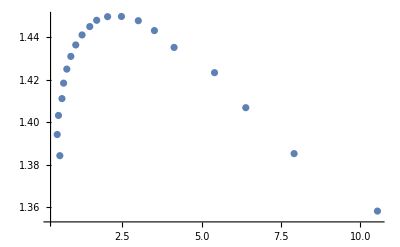

```mathematica
{α=0,β=-4*10^-4,κ=0,ρc=10^10*7.4262*10^-28,start=10^-5,zeroValue=0};
list={};SetSharedVariable[list];
ParallelDo[sol=NDSolve[{D[q[x],x]/r0==4*Pi*(r0*x)^2*(α*ρ[x])*(1-(2*Msun*y[x])/(r0*x)+(q[x]/(r0*x))^2)^(-1/2),Msun/r0*D[y[x],x]==4*Pi*(r0*x)^2*ρ[x]+β/2*(r0*x)^2*(3*ρ[x]-pr[ρ[x]])+(q[x]*D[q[x],x])/(x*r0^2),D[pr[ρ[x]],x]/r0==-(pr[ρ[x]]+ρ[x])/(1+a)*(4*Pi*(r0*x)*pr[ρ[x]]+(Msun*y[x])/(r0*x)^2-(β*r0*x)/2*(ρ[x]-3*pr[ρ[x]])-q[x]^2/(r0*x)^3)*(1-(2*Msun*y[x])/(r0*x)+(q[x]/(r0*x))^2)^(-1)+2/(1+a)*(κ*pr[ρ[x]])/(r0*x)*((2*Msun*y[x])/(r0*x)-q[x]^2/(r0*x)^2)+a/(1+a)*D[ρ[x],x]/r0+(1-2*a)/(1+a)*q[x]/(4*Pi*(r0*x)^4)*D[q[x],x]/r0,q[start]==zeroValue,y[start]==zeroValue,ρ[start]==10^i*7.4262*10^-28},{q,y,ρ},{x,start,12.}]//Quiet;radius=x/.FindRoot[Re@pr[ρ[x]]/.sol,{x,0.5}]//Quiet;mass=Re@y[radius]/.sol[[1]]//Quiet;AppendTo[list,{radius,mass,i}],{i,11.,15.,.21}]
ListPlot[Thread[{list[[All,1]],list[[All,2]]}],PlotRange->All]
```